```mathematica
Get["C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\Mathematica\\CDTFunctions.wl"]
```

```mathematica
data = Import["C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\data\\Statistical_Volume_32768_TimeSize_128_stepsize_20001_sample_2.csv"]
```

```mathematica
Length[data]
```

100000

```mathematica
sorted = SortBy[data,-#[[2]]&];
```

```mathematica
sorted[[234]]
```

{450_389_367_338_354_349_326_316_307_296_285_250_227_221_189_202_193_206_193_195_191_181_186_178_173_158_170_136_147_140_137_121_117_103_70_57_61_50_59_67_69_75_59_47_39_42_32_26_23_30_36_26_34_34_39_34_26_25_18_31_41_44_65_51_45_46_69_79_75_73_95_115_111_122_107_101_91_108_89_94_83_95_77_78_86_81_65_71_63_55_56_45_58_75_92_110_114_129_123_160_177_155_131_135_172_178_165_194_188_189_200_194_169_155_157_129_127_114_143_127_110_128_155_178_200_164_149_178,41711.6}

```mathematica
Mean[Table[N[Oscilatory[ToExpression@ StringSplit[sorted[[i,1]],"_"]]],{i,100}]]
```

8.36023

```mathematica
Mean[Table[N[Oscilatory[ToExpression@ StringSplit[sorted[[-i,1]],"_"]]],{i,100}]]
```

8.4767

```mathematica
Oscilatory[l_]:=Sqrt[Mean[Differences[l]^2]]
```

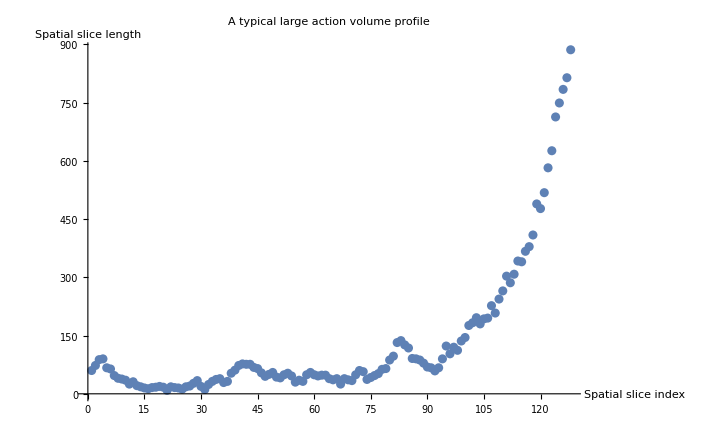

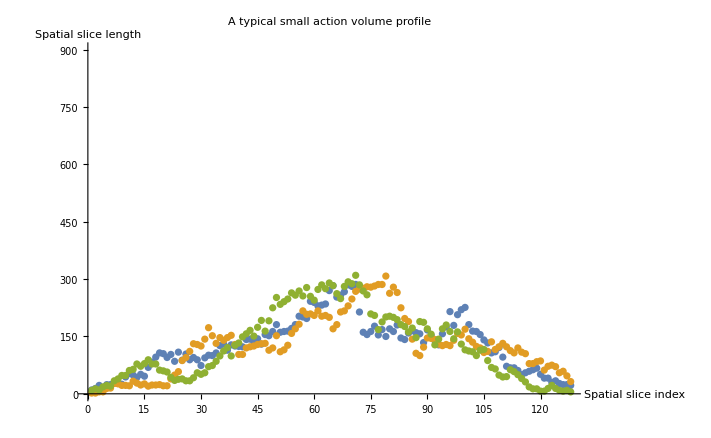

```mathematica
ListPlot[Table[N[ToExpression@ StringSplit[sorted[[i,1]],"_"]],{i,1}],PlotRange->All,AxesLabel->{"Spatial slice index","Spatial slice length"},PlotLabel -> "A typical large action volume profile" ]
ListPlot[Table[N[ToExpression@ StringSplit[sorted[[-i,1]],"_"]],{i,3}],AxesLabel->{"Spatial slice index","Spatial slice length"},PlotLabel -> "A typical small action volume profile" ,PlotRange->{0,900}]
```

```mathematica
a =Labeled[ DistributionChart[Transpose[Table[N[ToExpression@ StringSplit[sorted[[-i,1]],"_"]],{i,1000}]],PlotRange->{0,1028},ChartElementFunction->ChartElementData["Density"],ChartStyle-> {Directive[EdgeForm[None],Orange]},BarSpacing->0,PlotRange->All,PlotLabel-> "The smallest 1000 action in the sample"](*{ "The Smallest 1000 action in the sample",Style["Spatial slice index",8],Style["Spatial slice length",8]},{Top,{Right, Bottom},{Top , Left}}*),""
]
```

-Graphics-

```mathematica
sorted[[-1,2]]
sorted[[1,2]]
```

30191.6

46724.5

```mathematica
b = DistributionChart[Transpose[Table[N[ToExpression@ StringSplit[sorted[[i,1]],"_"]],{i,1000}]],PlotRange->{0,1028},ChartElementFunction->ChartElementData["Density"], ChartStyle-> {Directive[EdgeForm[None],Blue]},BarSpacing->0,PlotLabel-> "The Largest 1000 action in the sample"(*<>ToString[sorted[[-1,2]]]<>"-"<>ToString[sorted[[-100,2]]]*),PlotRange->All,AxesLabel->{"Spatial slice index","Spatial slice length"}]
```

-Graphics-

```mathematica
b = DistributionChart[Transpose[Table[N[ToExpression@ StringSplit[sorted[[RandomInteger[100000],1]],"_"]],{i,10000}]],PlotRange->{0,1028},ChartElementFunction->ChartElementData["Density"], ChartStyle-> {Directive[EdgeForm[None],Blue]},BarSpacing->0,PlotRange->All]
```

-Graphics-